# Positivity scheme

## F2 NC DIS

### Gluon coefficient function

```mathematica
Pqgx[z_]:=2((1-z)^2 + z^2)
cgx[z_]:={-2+16z(1-z),Pqgx@z Log[(1-z)/z]}
```

```mathematica
Pqgmx[m_,z_]:=z^m *Pqgx@z
PqgLogOmXx[z_]:=Log[1-z]*Pqgx@z
```

```mathematica
cgN[n_]:=Evaluate@Integrate[z^(n-1)*cgx[z], {z,0,1}, Assumptions->Re[n]>0]
```

```mathematica
PqgmN[m_,n_]:=Evaluate@Integrate[z^(n-1)*Pqgmx[m,z], {z,0,1}, Assumptions->Re[n]>0]
PqgLogOmXN[n_]:=Evaluate@Integrate[z^(n-1)*PqgLogOmXx[z], {z,0,1}, Assumptions->Re[n]>0]
```

```mathematica
Series[cgN@n,{n,∞,1}]
```

{-2/n+O[1/n]^2,(-2 EulerGamma+2 Log[1/n])/n+O[1/n]^2}

```mathematica
Series[PqgmN[m,n],{n,∞,1}]
Series[PqgLogOmXN[n],{n,∞,1}]
```

ConditionalExpression[2/(m+n)-4/(1+m+n)+4/(2+m+n),Re[m+n]>0]

(-2 EulerGamma+2 Log[1/n])/n+O[1/n]^2

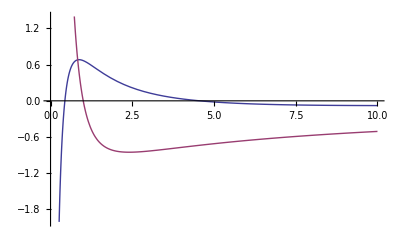

```mathematica
Plot[Evaluate@cgN@n, {n, 0, 10}]
```

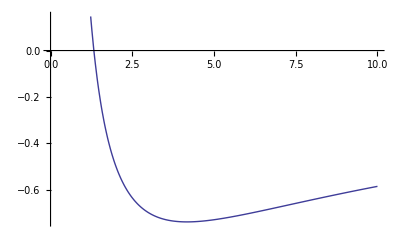

```mathematica
Plot[Plus@@cgN@n, {n, 0, 10}]
```

```mathematica
Series[Plus@@cgN@n - PqgLogOmXN[n],{n,∞,4}]
```

-2/n+18/n^2-56/n^3+148/n^4+O[1/n]^5

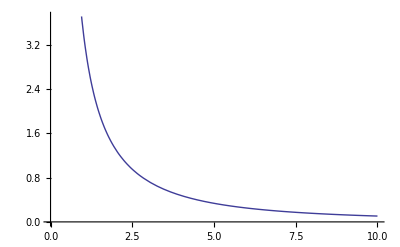

```mathematica
Plot[Plus@@cgN@n- PqgLogOmXN@n+PqgmN[0,n], {n, 0, 10}]
```

```mathematica
FullSimplify[(Plus@@cgN@n - PqgLogOmXN@n+PqgmN[0,n])>0,Assumptions->n>0]
```

True

#### Compare to Vogt et al.

```mathematica
s1[n_] := Evaluate@Sum[1/k, {k,1,n}]
s2[n_] := Evaluate@Sum[1/k^2, {k,1,n}]
s1c1[n_] := Evaluate@Sum[s1@k/k, {k,1,n}]
```

```mathematica
gqg[f_, n_] := 2f[n+2] - 4f[n+1] - f[n-1] + 3f[n]
```

```mathematica
vogtcg [n_] := -2 (gqg[s1c1 , n] + 4gqg[s1,n]-gqg[s2,n]) -6(s1[n-1] - s1[n])
```

```mathematica
FullSimplify[vogtcg[n] - Plus@@cgN@n]
```

0

### Quark coefficient function

```mathematica
cqRegx[z_]:=(6+4z)
cqDeltax=-(9+4Zeta[2]);
cqL1x[z_]:=-2(1+z)Log[(1-z)];
cqL0x[z_]:=2(1+z)Log[z] - 4 Log[z]/(1-z);
cqD0x[z_]:= -3/(1-z);
cqD1x[z_]:=4Log[1-z]/(1-z)
```

```mathematica
cqRegN[n_] := Evaluate@Integrate[cqRegx@z z^(n-1) ,{z,0,1}, Assumptions->Re[n]>0];
cqDeltaN = cqDeltax;
cqL1N[n_] := Evaluate@Integrate[cqL1x@z z^(n-1) ,{z,0,1}, Assumptions->Re[n]>0];
cqL0N[n_] := Evaluate@Integrate[cqL0x@z z^(n-1) ,{z,0,1}, Assumptions->Re[n]>0];
```

```mathematica
cqD0N[n_] := Evaluate@Integrate[cqD0x@z(z^(n-1)-1) ,{z,0,1}, Assumptions->Re[n]>0];
cqD1N[n_] := Evaluate@Integrate[cqD1x@z(z^(n-1)-1) ,{z,0,1}, Assumptions->Re[n]>0];
```

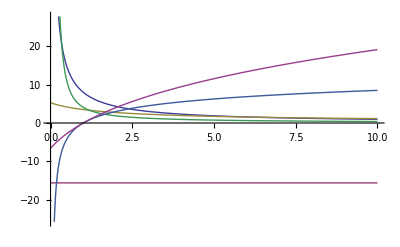

```mathematica
Plot[{cqRegN@n,cqDeltax,cqL1N@n,cqL0N@n,cqD0N@n,cqD1N@n}, {n,0,10}]
```

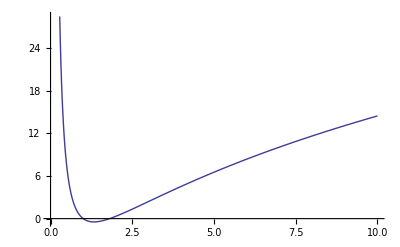

```mathematica
Plot[Plus@@{cqRegN@n,cqDeltax,cqL1N@n,cqL0N@n,cqD0N@n,cqD1N@n}, {n,0,10}]
```

```mathematica
Series[{cqRegN@n,cqDeltax,cqL1N@n,cqL0N@n,cqD0N@n,cqD1N@n}, {n,∞,1}]
```

{10/n+O[1/n]^2,-9-(2 π^2)/3,(4 EulerGamma-4 Log[1/n])/n+O[1/n]^2,4/n+O[1/n]^2,(3 EulerGamma-3 Log[1/n])-3/(2 n)+O[1/n]^2,(2 EulerGamma^2+π^2/3-4 EulerGamma Log[1/n]+2 Log[1/n]^2)+(-2-2 EulerGamma+2 Log[1/n])/n+O[1/n]^2}

#### Compare to Vogt et al.

```mathematica
gqq[f_, n_] := f[n+1] + f[n-1]
```

```mathematica
vogtcq[n_] := 9(s1@n-1) +2(gqq[s1c1,n]+2gqq[s1,n]-gqq[s2,n])-7(s1[n-1]+s1[n])
```

```mathematica
FullSimplify[vogtcq[n]-Plus@@{cqRegN@n,cqDeltax,cqL1N@n,cqL0N@n,cqD0N@n,cqD1N@n}]
```

0